Curate and Plot emission data from CDIAC

## Import Data

```mathematica
SetDirectory["/Users/tbury/Library/Mobile Documents/com~apple~CloudDocs/Research/climate_social"];
```

```mathematica
rawLanduse=Import["external_data/cdiac_landuse.xls","Data"];
rawFossil=Import["external_data/cdiac_fossilfuel.csv","Data"];
rawTemp=Import["/Users/tbury/Library/Mobile Documents/com~apple~CloudDocs/Research/climate_social/external_data/GLB.Ts+dSST.csv","Data"];
rawPop=Import["/Users/tbury/Library/Mobile Documents/com~apple~CloudDocs/Research/climate_social/external_data/global_pop.csv","Data"][[11802;;,;;]];
```

### Graphing Options

```mathematica
opts={Frame->True,LabelStyle->14,ImageSize->400};
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

## Global Co2 emissions

### Curate Data

```mathematica
(* co2 emissions from change in land use *)
tValsLand=rawLanduse[[2,2;;,1]]; (* goes from 1850 to 2005 *)
co2LandSeries=rawLanduse[[2,2;;,2]];
```

```mathematica
(* co2 emissions from burning fossil fuels *)
tValsFossil=rawFossil[[3;;,1]];
co2FossilSeries=rawFossil[[3;;,2]];
tValsFossilPc=rawFossil[[202;;,1]];
co2FossilPcSeries=rawFossil[[202;;,8]];
```

```mathematica
(* linear extrapolate data from 1850-1900 to give data from 1800-1850 *)
co2Land1850=co2LandSeries[[1]];
co2Land1900=co2LandSeries[[50]];
co2Land1800=2co2Land1850-co2Land1900;
```

```mathematica
(* linear extrapolate data from 1955-2005 to give data from 2005 to 2014 *)
co2Land1955=co2LandSeries[[105]];
co2Land2005=co2LandSeries[[-1]];
co2Land2014=(9/50)*(co2Land2005-co2Land1955)+co2Land2005;
```

```mathematica
co2Land1800
```

275.4

```mathematica
(* Prepend and Append co2Land with this data *)
co2LandSeriesMod=Append[Prepend[co2LandSeries,co2Land1800],co2Land2014];
tValsLandMod=Append[Prepend[tValsLand,1800],2014];
```

```mathematica
co2LandSeries//Dimensions
```

{156}

```mathematica
(* total co2 emissions data *)
co2TotSeries=Append[
Prepend[co2LandSeries+co2FossilSeries[[100;;255]],
co2Land1800+co2FossilSeries[[1]]],
co2Land2014+co2FossilSeries[[-1]]];
```

```mathematica
(* Export total co2 emissions data for use with model simulation *)
Export["export_data/historical_emissions.dat",{tValsLandMod,co2TotSeries*(10^(-3))}];
```

```mathematica
emissionLegend=LineLegend[TMBcolours[[1;;3]],{"Land-use","Fossil-fuel","Total"},LabelStyle->13]
```

### Plot of global emissions (linearly extrapolated land-use emissions)

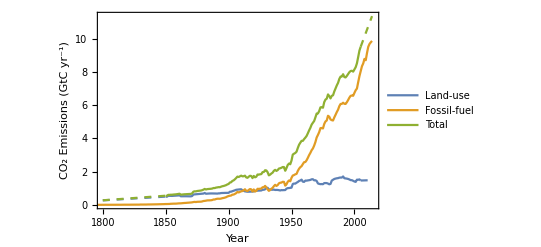

```mathematica
globalEmissionsPlot=ListLinePlot[{Transpose[{tValsLandMod[[2;;-2]],(10^(-3))*co2LandSeriesMod[[2;;-2]]}],
Transpose[{tValsLandMod[[1;;2]],(10^(-3))*co2LandSeriesMod[[1;;2]]}],
Transpose[{tValsLandMod[[-2;;-1]],(10^(-3))*co2LandSeriesMod[[-2;;-1]]}],
Transpose[{tValsFossil,10^(-3)*co2FossilSeries}],
Transpose[{tValsLandMod[[1;;2]],10^(-3)*co2TotSeries[[1;;2]]}],
Transpose[{tValsLandMod[[-2;;-1]],10^(-3)*co2TotSeries[[-2;;-1]]}],
Transpose[{tValsLandMod[[2;;-2]],10^(-3)*co2TotSeries[[2;;-2]]}]},
Frame->True,
PlotStyle->{TMBcolours[[1]],{TMBcolours[[1]],Dashed},{TMBcolours[[1]],Dashed},TMBcolours[[2]],{TMBcolours[[3]],Dashed},{TMBcolours[[3]],Dashed},TMBcolours[[3]]},
LabelStyle->14,
PlotRange->{{1800,2015},All},
ImageSize->400,
PlotLegends->Placed[emissionLegend,Scaled[{0.22,0.7}]],
FrameLabel->{{"CO_2 Emissions (GtC yr^-1)",""},{"Year",""}}]
```

```mathematica
(*Export["figures/globalEmissionsPlot.png",globalEmissionsPlot,ImageResolution->100];*)
```

### Global Temperature

```mathematica
(* global, annual average temperature *)
tValsTemp=rawTemp[[3;;,1]];
annualTempSeries=rawTemp[[3;;,14]];  (* temp above 1950-1980 base *)
annualTempSeriesInd=annualTempSeries+0.2;(* temp above 1850-1900 baseline *)
```

```mathematica
emissionPlot=ListLinePlot[Transpose[{tValsFossil,co2FossilSeries/1000}],
PlotRange->{{1850,2020},All},
ImageSize->600,
Frame->{{True,False},{True,False}},
FrameTicks->{{All,None},{All,None}},
FrameLabel->{{"CO_2 Emissions (gtC yr^-1)",""},{"Year",""}},
LabelStyle->14,
ImagePadding->{{50,50},{50,50}},
FrameLabel->{{"CO_2emissions (gtC yr^-1)",None},{"Year",None}},
PlotStyle->Dashed];
```

```mathematica
co2SeriesPc[[-1]]//N
```

1.35636

```mathematica
tempPlot=ListLinePlot[Transpose[{tValsTemp,(annualTempSeriesInd)}],
ImageSize->600,
PlotRange->{{1850,2020},All},
Frame->{{False,True},{False,False}},
FrameTicks->{{None,All},{None,None}},
FrameLabel->{{"d","Temperature Anomaly (°C)"},{"",""}},
LabelStyle->14,
AxesStyle->{Red,Automatic},
ImagePadding->{{50,50},{50,50}},
Epilog->Text[Style["1850-1900 Baseline",15,Red],Scaled[{0.85,0.25}]],
PlotStyle->{}];
```

```mathematica
Overlay[{emissionPlot,tempPlot}];
```

### World Population

```mathematica
tValsPop=rawPop[[;;,1]];
popSeries=rawPop[[;;,2]];
```

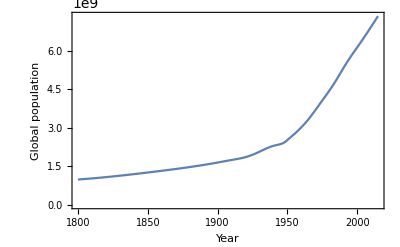

```mathematica
ListLinePlot[Transpose[{tValsPop,popSeries}],
LabelStyle->14,
Frame->True,
FrameLabel->{{"Global population",""},{"Year",""}}]
```

### Fossil fuel emissions per capita

```mathematica
(* co2FossilSeries is in MtC, put into tC per captia *)
```

```mathematica
co2SeriesPc=co2FossilSeries[[50;;]]*10^6/popSeries[[;;-2]];
tValsFossilPc=tValsFossil[[50;;]];
```

```mathematica
emissionPcPlot=ListLinePlot[Transpose[{tValsFossilPc,co2SeriesPc}],
PlotRange->{{1850,2020},All},
ImageSize->600,
Frame->{{True,False},{True,False}},
FrameTicks->{{All,None},{All,None}},
FrameLabel->{{"CO_2 Emissions per captia (tC yr^-1)",""},{"Year",""}},
LabelStyle->14,
ImagePadding->{{50,50},{50,50}},
PlotStyle->Dashed];
```

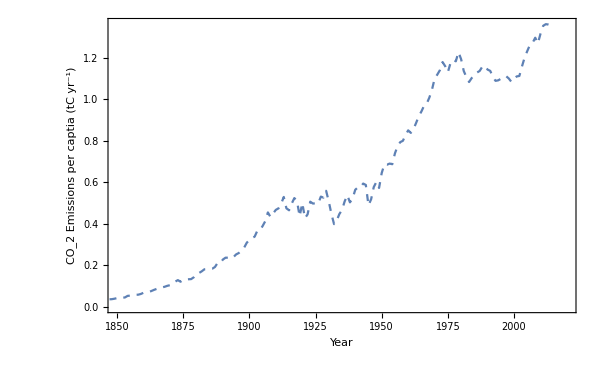
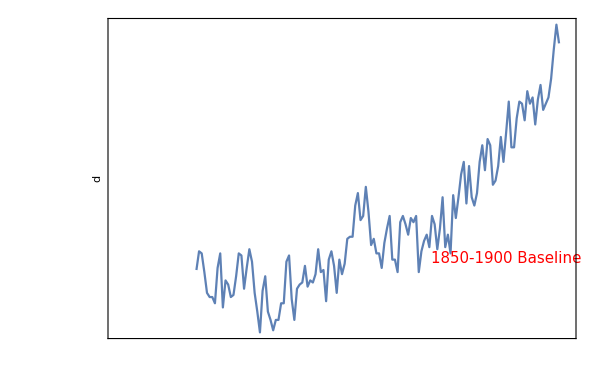

```mathematica
plotGlobalTempEmissions=Overlay[{emissionPcPlot,tempPlot}]
```

```mathematica
(*Export["figures/global_temp_emissions_percap.png",plotGlobalTempEmissions];*)
```

### Conversion factors

```mathematica
ka=1.773*^20; (* moles in atmosphere *)
gtcToMol=8.3259*^13;(* factor from gtC to moles *)
gtcToPpm=gtcToMol*10^6/ka; (* factor from gtc to ppmv *)
gtcTogtco2=3.664; (* factor from gtC from gtCO2 *)
secondstoyrs=60*60*24*365; (* factor from seconds to years *)
```

## Country-level Co2 emissions

```mathematica
rawFossilCountry=Import["/Users/tbury/Library/Mobile Documents/com~apple~CloudDocs/Research/climate_social/external_data/cdiac_fossilfuel_country.csv","Data"];

fossilCountryData=rawFossilCountry[[5;;]];
tableContents=rawFossilCountry[[1,;;]];
```

```mathematica
rawFossilCountry//Dimensions
```

{17236,10}

```mathematica
tableContents//TableForm
```

Nation
Year
Total CO2 emissions from fossil-fuels and cement production (thousand metric tons of C)
Emissions from solid fuel consumption
Emissions from liquid fuel consumption
Emissions from gas fuel consumption
Emissions from cement production
Emissions from gas flaring
Per capita CO2 emissions (metric tons of carbon)
Emissions from bunker fuels (not included in the totals)

```mathematica
{countries,countryFreq}=Tally[fossilCountryData[[;;,1]]]//Transpose;
```

```mathematica
(* function to split list into sublists of size given by elements of freq *)
partitionGen[list_,freq_]:=Table[list[[i]],{j,1,Length[freq]},{i,If[j==1,1,Total[freq[[1;;j-1]]]+1],Total[freq[[1;;j]]]}]
```

```mathematica
(* function to make first letter of string upper case *)
SetAttributes[makeFirstCap,Listable]
Clear[makeFirstCap]
makeFirstCap[string_]:=StringJoin[ReplacePart[Characters[string],1->ToUpperCase[Characters[string][[1]]]]]
```

```mathematica
(* function to take country string and output index *)
Clear[countryIndex]
countryIndex[string_]:=Position[countries,string][[1,1]]
```

```mathematica
countryIndex["UNITED KINGDOM"]
```

240

```mathematica
(* time values for each country time series *)
timeVals=partitionGen[fossilCountryData[[;;,2]],countryFreq];
```

```mathematica
(* emissions per capita for each country *)
emissionsCountryPerCap=partitionGen[fossilCountryData[[;;,9]],countryFreq];
```

```mathematica
(* total emissions for each country *)
emissionsCountry=partitionGen[fossilCountryData[[;;,3]],countryFreq];
```

### Plots

```mathematica
(* function to plot emissions per cap *)
Clear[emissionCountryPerCapPlot]
emissionCountryPerCapPlot[stringlist_]:=ListLinePlot[
Table[
Transpose[{timeVals[[countryIndex[stringlist[[i]]]]],emissionsCountryPerCap[[countryIndex[stringlist[[i]]]]]}],
{i,1,Length[stringlist]}],
PlotRange->{All,All},
Frame->True,
FrameLabel->{{"CO_2 Emissions per Capita (tC yr^-1)",""},{"Year",""}},
LabelStyle->14,
ImageSize->500,
PlotStyle->TMBcolours
]

(* function to plot total emissions *)
Clear[emissionCountryPlot]
emissionCountryPlot[stringlist_]:=ListLinePlot[
Table[
Transpose[{timeVals[[countryIndex[stringlist[[i]]]]],(10^(-6))*emissionsCountry[[countryIndex[stringlist[[i]]]]]}],
{i,1,Length[stringlist]}],
PlotRange->{{1900,2015},All},
Frame->True,
FrameLabel->{{"CO_2 Emissions (GtC yr^-1)",""},{"Year",""}},
LabelStyle->14,
ImageSize->500,
PlotStyle->TMBcolours
]
```

```mathematica
ClearAttributes[emissionCountryPerCapPlot,Listable]
```

```mathematica
(* list of countries of interest re: carbon emissions *)
myCountries={"UNITED ARAB EMIRATES","CHINA (MAINLAND)","CANADA","UNITED STATES OF AMERICA","UNITED KINGDOM","AUSTRALIA"};
```

```mathematica
legend=LineLegend[TMBcolours,myCountries]
```

## Country Specific Properties

### Countries with highest CO2 emissions (total not per capita)

```mathematica
totalEmissions={Total[emissionsCountry,{2}],countries}//Transpose;
```

```mathematica
topCountriesData=Sort[totalEmissions]//Reverse;
```

```mathematica
topCountriesData//TableForm;
```

```mathematica
topCountries=topCountriesData[[1;;10,2]];
```

```mathematica
topCountries
```

{UNITED STATES OF AMERICA,CHINA (MAINLAND),USSR,UNITED KINGDOM,JAPAN,GERMANY,INDIA,RUSSIAN FEDERATION,FRANCE (INCLUDING MONACO),CANADA}

```mathematica
multiEmissionCountryPlot=emissionCountryPlot[topCountries];
legend=LineLegend[TMBcolours,topCountries];
```

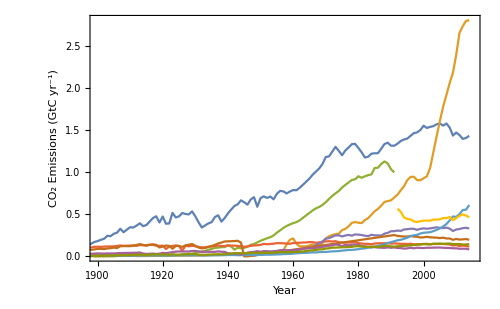
-Graphics- |

```mathematica
multiPlot1=Grid[{{multiEmissionCountryPlot,legend}}]
```

```mathematica
(*Export["figures/country_emission_data.png",multiPlot1];*)
```

```mathematica
(* the green curve stops at 1991 marking the dissolution of the Soviet Union. the yellow curve begins in 1992 marking the formation of the Russian federation *)
```

### Same countries on emissions per capita plot

```mathematica
multiEmissionCountryPerCapPlot=emissionCountryPerCapPlot[topCountries];
```

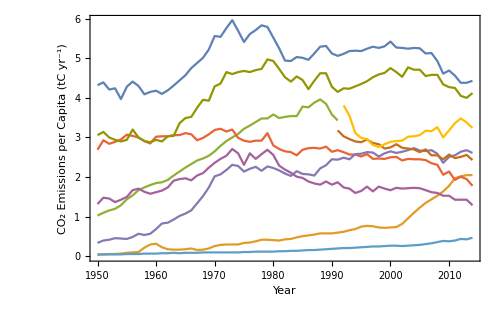
-Graphics- |

```mathematica
multiPlot2=Grid[{{multiEmissionCountryPerCapPlot,legend}}]
```

```mathematica
(*Export["figures/country_emission_percap_data.png",multiPlot2];*)
```